# Fitting the binding curve

## Reading the data

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
x=BinaryReadList["x2.dat","Real32"];
y=BinaryReadList["y2.dat","Real32"];
```

```mathematica
scatter=Table[{x[[i]],y[[i]]},{i,1,Length[x]}];
```

## Lennard-Jonnes (doesn’t work so well)

```mathematica
Clear[ϵ,σ]
nlm=Normal[NonlinearModelFit[scatter,4ϵ((σ/r)^12-(σ/r)^6),{ϵ,σ},r]]
```

0.398034 (0.0000290955/r^12-0.00539402/r^6)

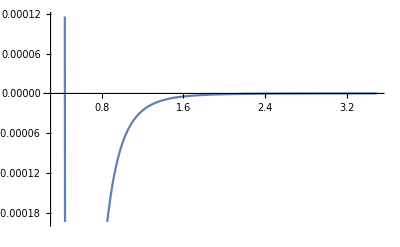

```mathematica
Clear[f]
f[r_]:=0.010619523843508963 (0.000053110959268918895/r^12-0.007287726618700713/r^6)
Show[Plot[f[r],{r,0.3,3.5}],ListPlot[scatter]]
```

## Morse (works very well)

```mathematica
nlm=Normal[NonlinearModelFit[scatter,De(Exp[-2a(r-re)]-2Exp[-a(r-re)]),{De,a,re},r]]
```

```mathematica
0.11431618298122724 (ⅇ^(-5.246522905831081 (-0.706041902090514+r))-2 ⅇ^(-2.6232614529155405 (-0.706041902090514+r)))
```

0.114316 (ⅇ^(-5.24652 (-0.706042+r))-2 ⅇ^(-2.62326 (-0.706042+r)))

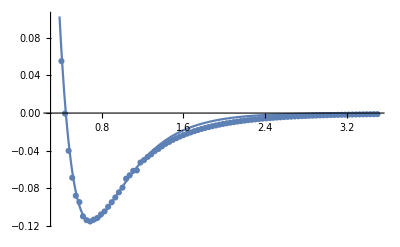

```mathematica
Clear[f]
f[r_]:=0.11576157896794113 (ⅇ^(-5.543231735551066 (-0.6998735296583554+r))-2 ⅇ^(-2.771615867775533 (-0.6998735296583554+r)))
Show[Plot[f[x],{x,0.3,3.5}],ListPlot[scatter]]
```